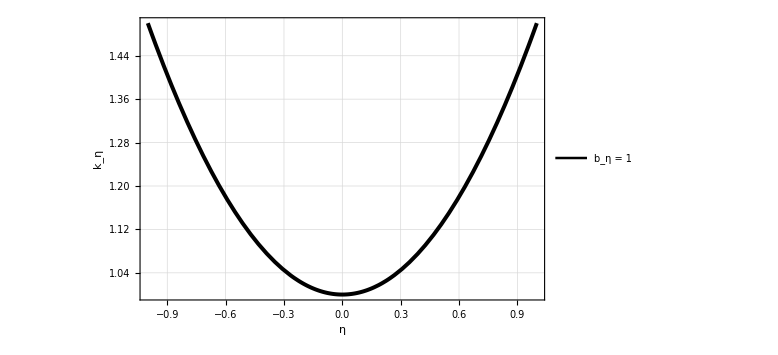

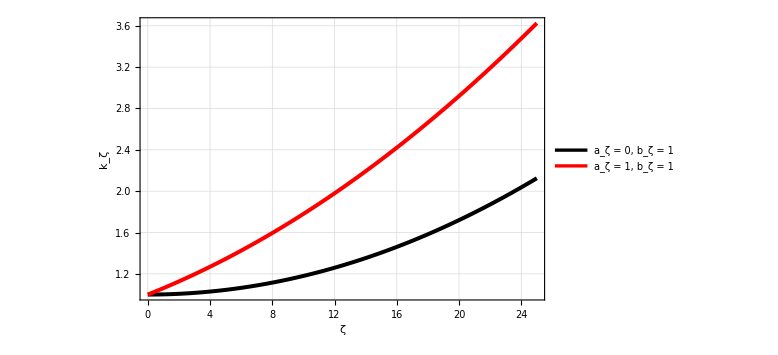

Getting the data...

Done.

μ_η

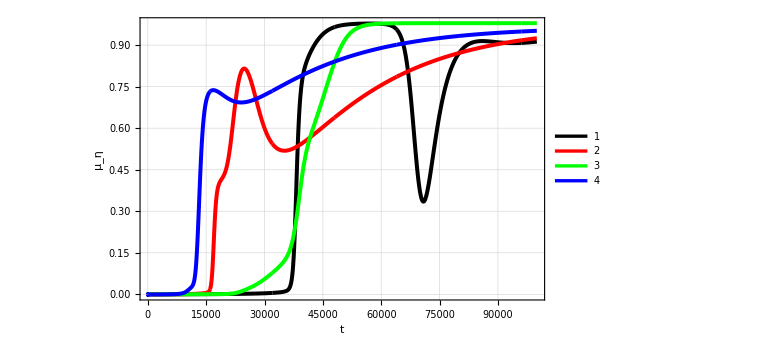

=========================================

μ_η

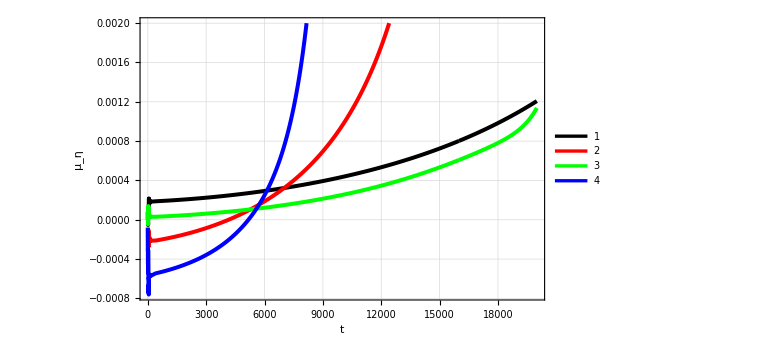

=========================================

μ_η

-Graphics-

=========================================

σ_η

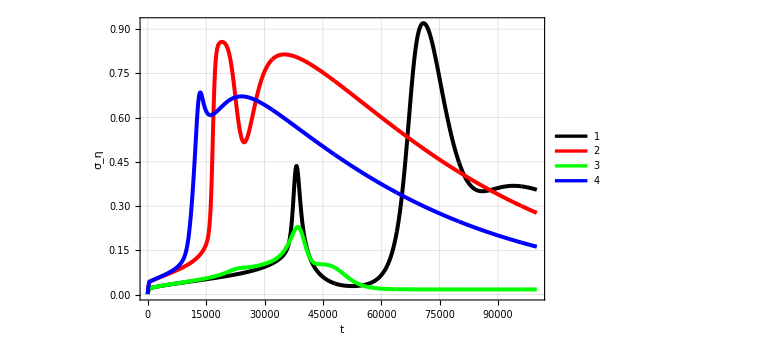

=========================================

μ_ζ

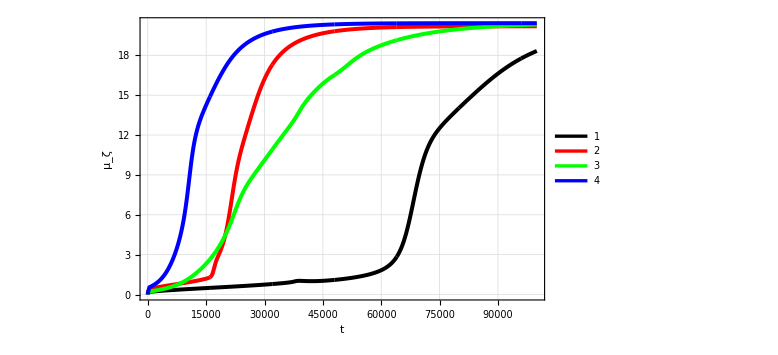

=========================================

σ_ζ

-Graphics-

=========================================

u_total

-Graphics-

=========================================

food

-Graphics-

=========================================

waste

-Graphics-

=========================================

```mathematica
(* Error in: mp_d500k1e01g01a005i10f1T, mp_d500k1e01g01a005i10f1P, mp_d500k1e01g01a005i10f1E *)
(* Based on mp_d500k1e01g01a005 instead of mp_d500k1e01g01a005i10 *)
(* Results in Chart #1 (error) == Chart #6 and in Chart #03 == Chart # 05 (error)  *)

kη[b_,η_]:=1+b*η^2/2;
kζ[a_,b_,scale_,ζ_]:=1+a*(ζ/scale)+b*(ζ/scale)^2/2;

scaleVal=(2/3)*25;

Plot[kη[1,η],{η,-1,1},Frame->True,GridLines->Automatic,ImageSize->Large,LabelStyle->{FontSize->16,Bold,Black},PlotStyle->{Black,Thickness[0.005]},FrameLabel->{{Subscript["k","η"],None},{"η",None}},PlotLegends->Placed[{Row[{Subscript["b","η"]," = 1"}]},{0.17,0.85}]]

(* ,PlotLegends -> Placed[LineLegend[Automatic,Row[{Subscript["b","η"]," = 1"}],LegendMarkerSize->{15,3}],{0.15,0.81}] *)

Plot[{kζ[0,1,scaleVal,ζ],kζ[1,1,scaleVal,ζ]},{ζ,0,25}, Frame -> True, GridLines->Automatic, ImageSize->Large,LabelStyle->{FontSize->16,Bold,Black},PlotStyle->{{Black, Thickness[0.005]},{Red, Thickness[0.005]}},FrameLabel->{{Subscript["k","ζ"],None},{"ζ",None}},PlotLegends -> Placed[LineLegend[Automatic,{Row[{Subscript["a","ζ"]," = 0, ",Subscript["b","ζ"]," = 1"}],Row[{Subscript["a","ζ"]," = 1, ",Subscript["b","ζ"]," = 1"}]},LegendMarkerSize->{15,3}],{0.15,0.81}]]

Print["Getting the data..."];
Get["C:\\GitHub\\CoreClm\\Math\\odePackChartSupport.m"];
Get["C:\\GitHub\\FindUniversity\\ClmFsharp\\ISSOL2023\\EeInf\\allData__200K.m"];
Print["Done."];

(* As in the file *)
(*
dataSource = { (* d500k1e01g01a005i10f1E$200K, *) d500k1e005g01a002f1E$200K,d500k1e005g01a002i10f1E$200K,d500k1e005g01a005f1E$200K,(* d500k1e005g01a005i10f1E$200K, *) d500k1e01g01a005f1E$200K, d500k1e01g01a002f1E$200K,d500k1e01g01a002i10f1E$200K,d500k1e01g01a005i10f1E$200K$Correct };
*)

(* In the order used in the article *)
dataSource = {  d500k1e005g01a002f1E$200K,d500k1e01g01a002f1E$200K,d500k1e005g01a002i10f1E$200K,d500k1e01g01a002i10f1E$200K
(*, d500k1e005g01a005f1E$200K, d500k1e01g01a005f1E$200K, d500k1e01g01a005i10f1E$200K$Correct *) };

dataSourceAll = {  d500k1e005g01a002f1E$200K,d500k1e01g01a002f1E$200K,d500k1e005g01a002i10f1E$200K,d500k1e01g01a002i10f1E$200K
, d500k1e005g01a005f1E$200K, d500k1e01g01a005f1E$200K, d500k1e01g01a005i10f1E$200K$Correct };

(*
(*
Print["1. ERROR: d500k1e01g01a005i10f1E$200K"];
plotCombinedChart[{d500k1e01g01a005i10f1E$200K},2,Subscript["μ","η"],divisor];
*)

Print["2. d500k1e005g01a002f1E$200K"];
plotCombinedChart[{d500k1e005g01a002f1E$200K},2,Subscript["μ","η"],divisor];

Print["3. d500k1e005g01a002i10f1E$200K - Chart #5 (error) should look like that."];
plotCombinedChart[{d500k1e005g01a002i10f1E$200K},2,Subscript["μ","η"],divisor];

Print["4. d500k1e005g01a005f1E$200K"];
plotCombinedChart[{d500k1e005g01a005f1E$200K},2,Subscript["μ","η"],divisor];

(*
Print["5. ERROR: d500k1e005g01a005i10f1E$200K"];
plotCombinedChart[{d500k1e005g01a005i10f1E$200K},2,Subscript["μ","η"],divisor];
*)

Print["6. d500k1e01g01a005f1E$200K - Chart #1 (error) should look like that."];
plotCombinedChart[{d500k1e01g01a005f1E$200K},2,Subscript["μ","η"],divisor];

Print["7. d500k1e01g01a002f1E$200K"];
plotCombinedChart[{d500k1e01g01a002f1E$200K},2,Subscript["μ","η"],divisor];

Print["8. d500k1e01g01a002i10f1E$200K"];
plotCombinedChart[{d500k1e01g01a002i10f1E$200K},2,Subscript["μ","η"],divisor];

Print["9. d500k1e01g01a005i10f1E$200K$Correct"];
plotCombinedChart[{d500k1e01g01a005i10f1E$200K$Correct},2,Subscript["μ","η"],divisor];

(* ================================================== *)
Print[sep];
Print[sep];
*)

divisor = 2;
shift = {0.9, 0.52};
plotCombinedChart[dataSource,2,Subscript["μ","η"],divisor, shift];

yScale:=0.002;
divisor = 10;
plotCombinedChartScaled[dataSource,2,Subscript["μ","η"],divisor, shift];

divisor = 2;
plotCombinedChart[dataSourceAll,2,Subscript["μ","η"],divisor, shift];
(* plotCombinedChart[dataSource,2,Subscript["μ","η"],divisor]; *)

plotCombinedChart[dataSource,3,Subscript["σ","η"],divisor,  {0.9, 0.65}];
plotCombinedChart[dataSource,4,Subscript["μ","ζ"],divisor, shift];
plotCombinedChart[dataSource,5,Subscript["σ","ζ"],divisor, shift];
plotCombinedChart[dataSource,7,Subscript["u","total"],divisor, shift];
plotCombinedChart[dataSource,8,"food",divisor, shift];
plotCombinedChart[dataSource,9,"waste",divisor, shift];
```